```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/sarp/Desktop/Binary_NS_detection_Work

## DATA from A-LIGO BNS Optimized, Einstein Telescope B Low-frequency end

#### ASD = 2 h̃(f) √f where h̃(f) is the Fourier transform of h(t)

```mathematica
ALIGO2017Data={{7*10^5,6000,100,20,4,2,1,0.9,0.8,0.9,1,2,4}*10^-23,{9,10,15,20,30,40,70,80,100,200,400,1000,1200}};
ALIGODesigndata={{10^5,10^4,100,32,20,15,8,5,2.35,1,0.6,0.4,0.3,0.25,0.3,0.8,3}*10^-23,{6,7,9,9.7,10,10.54,11.89,14,20,30,40,60,200,300,400,900,1200}};
ETdata={{10^6,500,135.6,65,50,40,20,14,6,3,2,1,0.5,0.15,0.06,0.03,0.025,0.03,0.07}*10^-23,{0.5,1,1.1090,1.175,1.2,1.3,1.5,2,3,4,5,7,10,20,30,60,150,300,1000}};
data={ALIGO2017Data,ALIGODesigndata,ETdata};
choice=3;
Ls=Table[Length[data[[i,1]]],{i,1,3}]
```

{13,17,19}

```mathematica
ThreeIFOData=Table[{data[[j,2,i]],data[[j,1,i]]},{j,1,Length[data]},{i,1,Ls[[j]]}];
```

```mathematica
GWFreqs=Table[ThreeIFOData[[j,i,1]],{j,1,Length[data]},{i,1,Ls[[j]]}];
```

```mathematica
ASDData=Table[ThreeIFOData[[j,i,2]],{j,1,Length[data]},{i,1,Ls[[j]]}];
```

```mathematica
ASDvFreqData=Table[{GWFreqs[[j,i]],ASDData[[j,i]]},{j,1,Length[data]},{i,1,Ls[[j]]}];
```

## Computation of accumulated phase using Blanchet 2014, 3.5-pN accurate expressions and Colpi-Sesana’s formulae

```mathematica
Clear[x,h]
```

```mathematica
nu[m1_,m2_]:=(m1 m2)/(m1+m2)^2
```

```mathematica
Mchirp[m1_,m2_,nu_]:=nu^(3/5)(m1+m2)Msun
```

```mathematica
X=(G M Ω/c^3)^(2/3);
Msun=1.989*10^30;
clight=299792458;
ν=1/4;
Mc=ν^(3/5)M;
fISCO=c^3/(6^(3/2)π G (m1+m2));
A=π^(-2/3)√(5/12);
AngAveFact=1/Pi Integrate[(1+Cos[i]^2)/2,{i,0,Pi}];
Mpc=10^6*360/(2π)*3600*149597870700.;
GWfreqIsco[mBH_]:=fISCO/.m2->(Msun mBH)/.G->6.67*10^-11/.m1->(1.4Msun)/.c->clight
fISCO/.G->6.67*10^-11/.(m1+m2)->(2.8Msun)/.c->clight
GWfreqIsco[1.4]
```

1570.97

1570.97

```mathematica
Simplify[nu[7/5,7/5Q]]
```

Q/(1+Q)^2

```mathematica
Mchirp[1.4,m2,Simplify[nu[7/5,7/5Q]]]
```

1.989×10^30 (1.4+m2) (Q/(1+Q)^2)^(3/5)

## Frequency and Time Domain Strains generated by the Binary

```mathematica
h̃=AngAveFact A c/LumDist(G Mc/c^3)^(5/6)GWFreqs^(-7/6)  ;(* strain in FD, Colpi-Sesana Eqs.(29-30) *)

h=AngAveFact 4/LumDist(G Mc/c^2)^(5/3)(π GWFreqs/c)^(2/3);(* strain in TD Colpi-Sesana Eqs.(29-30) *)
(h̃)/Mpc/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight;
h/Mpc/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight;
```

```mathematica
hFD[m2_,f_,D_]=Block[{G=6.67*10^-11,Q=m2/(1.4),c=clight},AngAveFact A c/D(G Mchirp[1.4,m2 ,Simplify[nu[7/5,7/5Q]]]/c^3)^(5/6)f^(-7/6)]
hTD[m2_,f_,D_]=Block[{G=6.67*10^-11,Q=m2/(1.4),c=clight},AngAveFact 4/D(G Mchirp[1.4,m2 ,Simplify[nu[7/5,7/5Q]]]/c^2)^(5/3)(π f/c)^(2/3)]
```

(3022.2 ((1.4+m2) (m2/(1.4+1. m2)^2)^(3/5))^(5/6))/(D f^(7/6))

(3.84888 f^(2/3) ((1.4+m2) (m2/(1.4+1. m2)^2)^(3/5))^(5/3))/D

```mathematica
hFD[1.4,100,40Mpc]
```

1.1327×10^-23

## Inspiral time, accumulated phase: 0PN and 2PN expressions

```mathematica
Tinsp0PN[fin_,m2_]:=5/(256 π^(8/3))1/ν(c^3/(G (m1+m2)Msun))^(5/3)fin^(-8/3)/.G->6.67*10^-11/.m1->(1.4)/.c->clight;
Phi0PN[fin_,m2_]:=2(5G Mchirp[1.4,m2 ,Simplify[nu[7/5,7/5Q]]]/c^3)^(-5/8)Tinsp0PN[fin]^(5/8)/.G->6.67*10^-11/.m1->(1.4)/.c->clight/.Q->m2/1.4;
Ncycles0PN[fin_,m2_]:=1/(32 π^(8/3))(G Mchirp[1.4,m2 ,Simplify[nu[7/5,7/5Q]]]/c^3)^(-5/3)(fin^(-5/3)-GWfreqIsco[m2]^(-5/3))/.G->6.67*10^-11/.m1->(1.4)/.c->clight/.Q->m2/1.4;
```

```mathematica
VertLine1=Line[{{1,Log[0.0001]},{1,Log[(1+Q)^(1/3)/Q/.Q->1]}}];
VertLine2=Line[{{(3.81/1.4),Log[0.0001]},{(3.81/1.4),Log[(1+Q)^(1/3)/Q/.Q->(3.81/1.4)]}}];
VertLine3=Line[{{(27.4/1.4),Log[0.0001]},{(27.4/1.4),Log[(1+Q)^(1/3)/Q/.Q->(27.4/1.4)]}}];
```

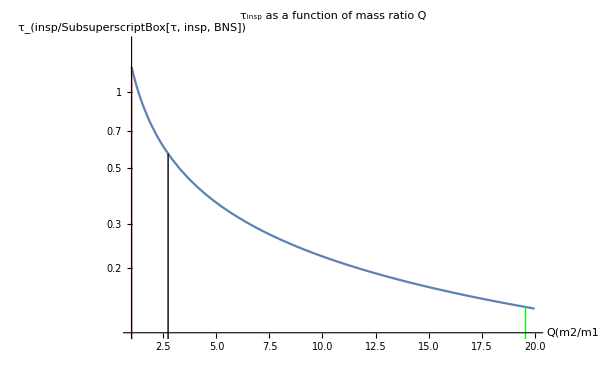

```mathematica
LogPlot[{(1+Q)^(1/3)/Q},{Q,1,20},PlotRange->All,PlotLabel->"τ_insp as a function of mass ratio Q",AxesLabel->{"Q(m2/m1)","τ_(insp/SubsuperscriptBox[τ, insp, BNS])"},Epilog->{{Directive[Red],VertLine1},VertLine2,{Directive[Green,Thick],VertLine3}},ImageSize->600]
```

### 2PN expressions from Section 5.6.4 of Maggiore’s Book

```mathematica
τ0[f_,m2_]:=5/(256 ν f π)(π G ((m1+m2)Msun)/c^3 f)^(-5/3)/.G->6.67*10^-11/.m1->(1.4)/.c->clight;
τ1[f_,m2_]:=5/(192 ν f π)(π G ((m1+m2)Msun)/c^3 f)^-1(743/336+11/4 ν)/.G->6.67*10^-11/.m1->(1.4)/.c->clight;
τ15[f_,m2_]:=1/(8 ν f)(π G ((m1+m2)Msun)/c^3 f)^(-2/3)/.G->6.67*10^-11/.m1->(1.4)/.c->clight;
τ2[f_,m2_]:=5/(128 ν f π)(π G ((m1+m2)Msun)/c^3 f)^(-1/3)(3058673/1016064+5429/1008 ν+617/144 ν^2)/.G->6.67*10^-11/.m1->(1.4)/.c->clight;
```

```mathematica
Tinsp2PN[f_,fin_,m2_]:=τ0[fin,m2](1-(f/fin)^(-8/3))+τ1[fin,m2](1-(f/fin)^-2)-τ15[fin,m2](1-(f/fin)^(-5/3))+τ2[fin,m2](1-(f/fin)^(-4/3));
Phi2PN[f_,fin_,m2_]:=16 π/5 fin(τ0[fin,m2] (1-(f/fin)^(-5/3))+5/4 τ1[fin,m2](1-(f/fin)^-1)-25/16 τ15[fin,m2](1-(f/fin)^(-2/3))+5/2 τ2[fin,m2](1-(f/fin)^(-1/3)));
```

## Definining the SNR with the gain factor R included from m_2> m_1

```mathematica
Snoise=Table[Interpolation[ASDvFreqData[[i]],InterpolationOrder->1],{i,1,Length[data]}];
SNR[i_,fi_,ff_,D_,m2_]:=NIntegrate[4( hFD[m2,f,D])^2/(Snoise[[i]][f])^2,{f,fi,ff}]^(1/2)
```

## BINARY BH-NS Systems

### Tidal Tearing

```mathematica
BHspin={0,0.5,0.75,0.9,1};
```

```mathematica
Series[1/(1-ϵ)^2-1/(1+ϵ)^2,{ϵ,0,7}]
```

4 ϵ+8 ϵ^3+12 ϵ^5+16 ϵ^7+O[ϵ]^8

```mathematica
(0.5/0.3^2)^(1/3)
```

1.7711

```mathematica
%^(3/2)
```

2.35702

```mathematica
%*4/3
```

3.1427

```mathematica
1.4/8
```

0.175

```mathematica
MBHmax=1/√(6^3/2 1.4/(1.7 8)^3)
```

4.0788

```mathematica
MBHmax/1.4
```

2.91343

```mathematica
1.35/(15.2/1.5)
```

0.133224

```mathematica
(*Eq. (12) *)
```

```mathematica
4.6 1 (12/10)^(3/2)
```

6.04686

```mathematica
%/1.4
```

4.31918

```mathematica
(G Msun/({9900,11200,11500}clight^2))/.G->6.67 10^-11
```

{0.149102,0.131796,0.128358}

```mathematica
5/1.4
```

3.57143

```mathematica
10000/(G Msun/clight^2)/.G->6.67 10^-11
```

6.77456

```mathematica
1.4/%
```

0.206656

```mathematica
CM={4.6,7.8,12,19,68};
```

```mathematica
MBHmaxTD[Cm_,Cns_]=Cm/2.5(1/5)^(3/2)Cns^(-3/2);
MBHmaxMS[Cm_,Cns_]=5 Cm/9(1/5)^(3/2)Cns^(-3/2);
```

```mathematica
MBHmaxTD[CM,0.175]
MBHmaxMS[CM,0.175]
```

{2.24805,3.81191,5.86448,9.28542,33.232}

{3.12229,5.29432,8.1451,12.8964,46.1556}

```mathematica
(* Numerically determined ISCO Ω and radii *)
```

```mathematica
Block[{CNS=0.175},0.068/(1.4+Mbh)(1-0.444(1.4/Mbh)^(1/4)(1-3.54 CNS^(1/3)))/.Mbh->MBHmaxTD[CM,CNS]]
```

{0.0258457,0.0174668,0.0122079,0.00808942,0.0023506}

```mathematica
%^(-2/3)
```

{11.4395,14.8545,18.8614,24.8154,56.565}

```mathematica
6.^(-3/2)
```

0.0680414

```mathematica
(* Sch ISCO from NR *)
```

```mathematica
Block[{CNS=0.175},6(1+1/Q)/((1-0.444(Q)^(-1/4)(1-3.54 CNS^(1/3)))^(2/3))/.Q->{5,6,10}]
```

{6.07268,5.94386,5.70382}

```mathematica
(*Kerr ISCO Calculations*)
```

```mathematica
Z1[a_]=1+(1-a^2)^(1/3)((1+a)^(1/3)+(1-a)^(1/3));
Z2[a_]=(3 a^2+Z1[a]^2)^(1/2);
```

```mathematica
rLSO[a_]=3+Z2[a]-√((3-Z1[a])(3+Z1[a]+2Z2[a]));
```

```mathematica
rLSO[BHspin]
```

{6,4.233,3.15804,2.32088,1}

```mathematica
ΩLSO[a_]=(√rLSO[a])/(rLSO[a]^2+a √rLSO[a]);
```

```mathematica
ΩLSO[{0.,0.5,0.75,0.9,1}]
```

{0.0680414,0.108588,0.157181,0.225442,1/2}

```mathematica
MBHmaxMSv2=1/√(0.7 (rLSO[{0,0.5,0.75,0.9,1}]/(1.7 8))^3)
```

{4.0788,6.88314,10.6815,16.9543,59.9459}

```mathematica
(*From Fig. 5 of arXiv:0801.4297*)
```

```mathematica
MbhTD={40,20,10,2.5}; 
fTD={520,640,710,790};
aTD={0.98,0.85,0.5,0};
```

```mathematica
rTD[f_,a_,m_]=(-a+c^3/(G(1.4+m)*Msun f π))^(2/3)/.G->6.67*10^-11/.c->clight; (* from Kerr ISCO frequency formula *)
```

```mathematica
rTD[fTD,aTD,MbhTD]
```

{1.59952,2.46502,3.82715,7.60746}

```mathematica
rLSO[aTD]
```

{1.61403,2.6321,4.233,6}

```mathematica
Mbhv3=Table[NSolve[rTD[fTD[[i]],aTD[[i]],M]==rLSO[aTD[[i]]],M][[1,1,2]],{i,1,Length[aTD]}]
```

{39.6231,18.3279,8.48727,4.16798}

```mathematica
Table[{aTD[[i]],Mbhv3[[i]]},{i,1,Length[aTD]}]
```

{{0.98,39.6231},{0.85,18.3279},{0.5,8.48727},{0,4.16798}}

```mathematica
MassData={MBHmaxTD[CM,0.175],MBHmaxMS[CM,0.175],MBHmaxMSv2};
```

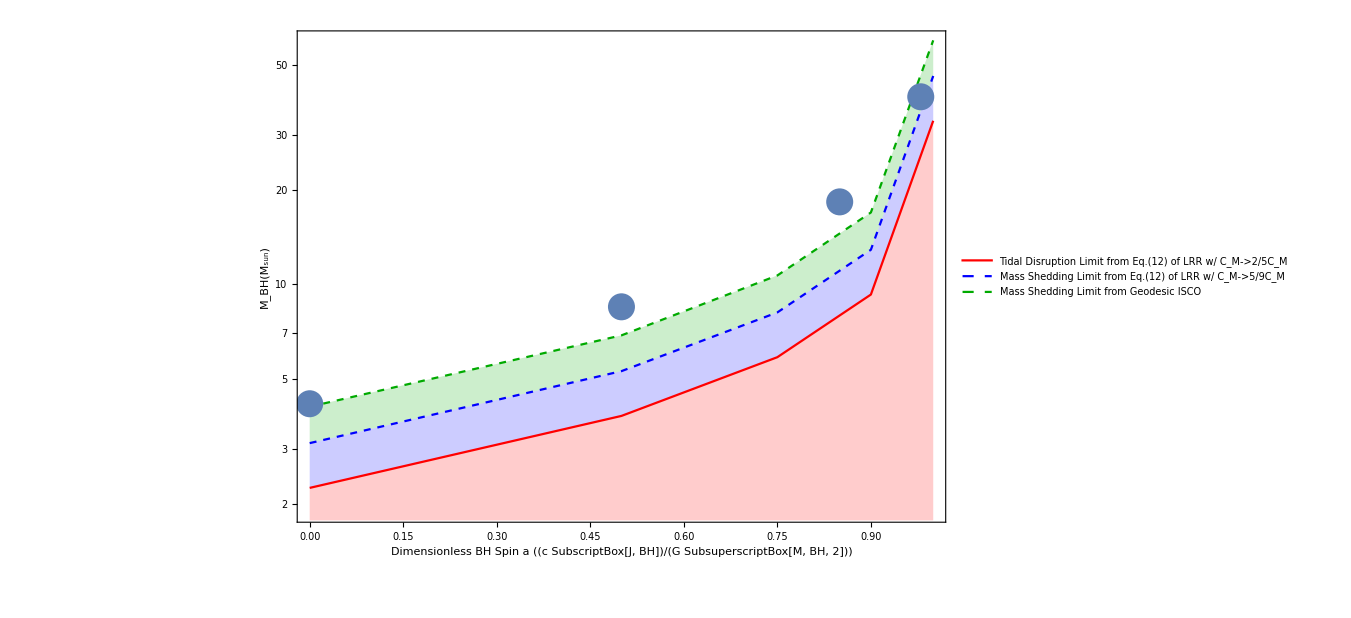

```mathematica
Show[ListLogPlot[Table[{BHspin[[i]],MassData[[j,i]]},{j,1,Length[MassData]},{i,1,Length[BHspin]}],Joined->True,PlotStyle->{Red,{Dashed,Blue},{Dashed,Darker[Green]}},Filling->{1->Axis,2->{1},3->{2}},
PlotLegends->Placed[LineLegend[{"Tidal Disruption Limit from Eq.(12) of LRR w/ C_M->2/5C_M","Mass Shedding Limit from Eq.(12) of LRR w/ C_M->5/9C_M","Mass Shedding Limit from Geodesic ISCO"},LegendFunction->"Frame"],{0.25,0.85}],
ImageSize->1000,Frame->True,FrameLabel->{"Dimensionless BH Spin a ((c SubscriptBox[J, BH])/(G SubsuperscriptBox[M, BH, 2]))","M_BH(M_sun)"},FrameStyle->Directive[24,AbsoluteThickness[3]],FrameTicksStyle->Directive[Black,24]],ListLogPlot[Table[{aTD[[i]],Mbhv3[[i]]},{i,1,Length[aTD]}]]]
```

### GWs STRAIN SCALING in TERMS of MASS RATIO Q ≥ 1

```mathematica
(* Mass ratio Q for a 1.4 Subscript[M, sun] NS *)
MBHmaxTD[CM,0.175]/1.4
```

{1.60575,2.72279,4.18891,6.63244,23.7372}

```mathematica
FullSimplify[Mchirp[m1,m2,nu[m1,m2]]/Msun/.m2->Q m1]
```

1. m1 (Q/(1+Q)^2)^(3/5) (1+Q)

```mathematica
Mc56[Q_]=FullSimplify[Mchirp[m1,m2,nu[m1,m2]]^(5/6)/Msun^(5/6)/.m2->Q m1,Q>1]
```

(1. m1^(5/6) √Q)/(1+Q)^(1/6)

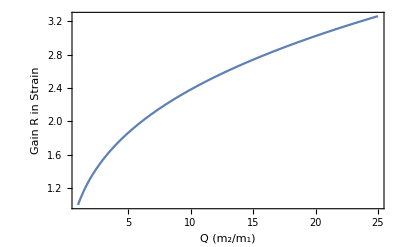

```mathematica
Plot[Mc56[Q]/Mc56[1],{Q,1,25},FrameLabel->{"Q (m_2/m_1)","Gain R in Strain"},Frame->True]
```

```mathematica
GainASDFactors=Mc56[MBHmaxTD[CM,0.175]/1.4]/Mc56[1]
```

{1.21252,1.48776,1.74599,2.06015,3.20377}

## CHECKS: GW170817 at A-LIGO 2017 Swept from 30 Hz to ~ 2000 Hz in 60 seconds and ~ 3000 cycles with SNR = 32.4

```mathematica
fin=30;
fout=300;
SNR300Hz=SNR[1,fin,fout,40Mpc,1.4];
SNR1200Hz=SNR[1,fin,GWfreqIsco[1.4],40Mpc,1.4];
Print["SNR(40 -> 300Hz) = ", SNR300Hz]
Print["SNR(40 -> f_ISCO) = ", SNR1200Hz]
Print["Inspiral time = ", Tinsp0PN[fin,1.4] ,"(0 PN) + ",Tinsp2PN[GWfreqIsco[1.4],fin,1.4]-Tinsp0PN[fin,1.4], "(2PN) = ",Tinsp2PN[GWfreqIsco[1.4],fin,1.4]," seconds"]
Print["𝒩_cycles = ", Ncycles0PN[fin,1.4],"(0 PN) + ",Phi2PN[GWfreqIsco[1.4],fin,1.4]/(2π)-Ncycles0PN[fin,1.4], "(2PN) = ",Phi2PN[GWfreqIsco[1.4],fin,1.4]/(2π)]
```

SNR(40 -> 300Hz) = 32.7054

SNR(40 -> f_ISCO) = 33.5743

Inspiral time = 53.5763(0 PN) + 1.13559(2PN) = 54.7119 seconds

𝒩_cycles = 2568.15(0 PN) + 53.8213(2PN) = 2621.98

## (3.81 M_sun, a=0.5) BH - NS

```mathematica
mBH=MBHmaxTD[CM,0.175][[2]]
```

3.81191

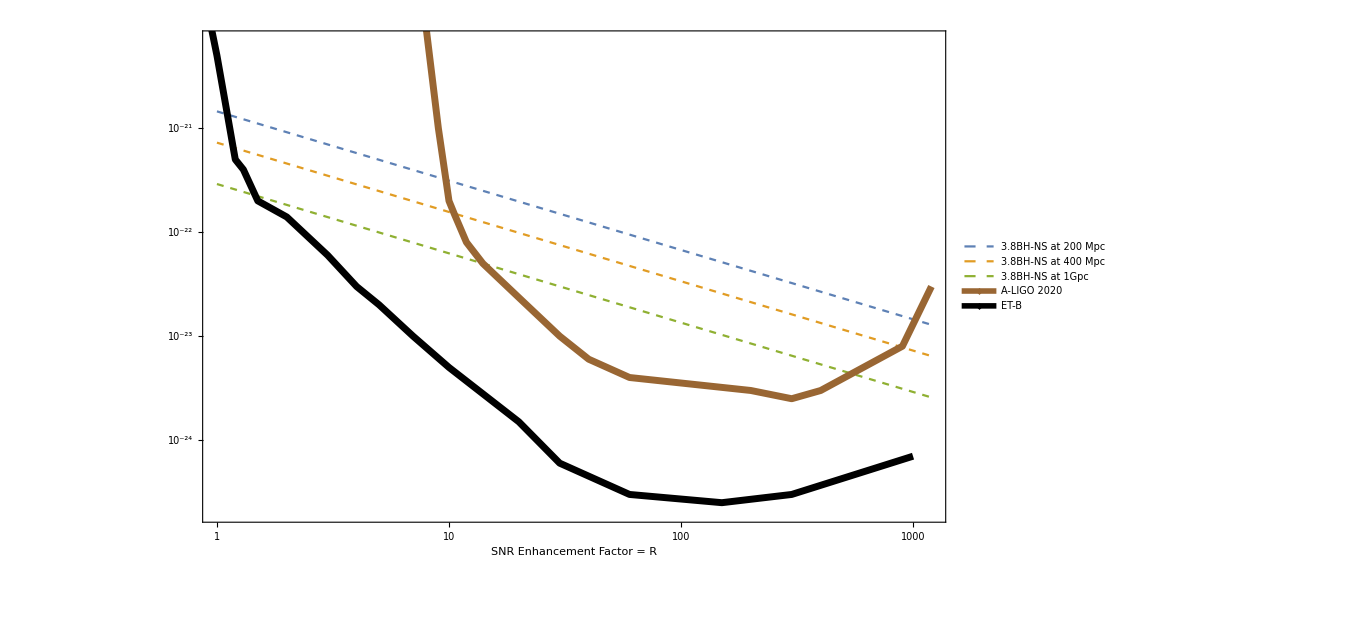

```mathematica
ASDPlotsBHNS=Show[LogLogPlot[{2 √f hFD[mBH,f,200Mpc],2 √f hFD[mBH,f,400Mpc],2 √f hFD[mBH,f,1000Mpc]},{f,1,1200},PlotStyle->{Dashed,Dashed,Dashed},PlotRange->{{1,1200},{2 10^-25,7 10^-21}},PlotLegends->{"3.8BH-NS at 200 Mpc","3.8BH-NS at 400 Mpc","3.8BH-NS at 1Gpc"}],ListLogLogPlot[{ASDvFreqData[[2]],ASDvFreqData[[3]]},Joined->True,PlotStyle->{{Thickness[0.005],Brown},{Thickness[0.005],Black}},AxesLabel->{"GW freq.",None},PlotLegends->PointLegend[{"A-LIGO 2020","ET-B"},LegendMarkers->"◆",LegendMarkerSize->{{5,25}}]],ImageSize->1000,Frame->True,FrameLabel->"SNR Enhancement Factor = "<>ToString[R]]
```

## (3.81 M_sun) BH - NS(200, 400 Mpc) at A-LIGO2020

### Picking out the LIGO-band entrance frequencies for M_BH=3.81

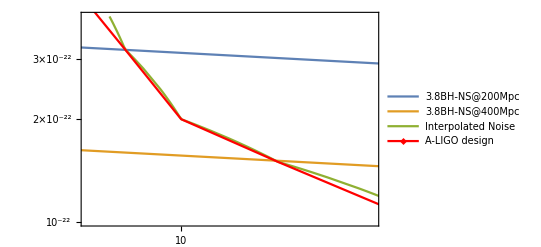

```mathematica
Show[LogLogPlot[{2 √f hFD[mBH,f,200Mpc],2 √f hFD[mBH,f,400Mpc],Snoise[[2]][f]},{f,6,200},PlotStyle->{Automatic},PlotRange->{{9.5,11.1},{1. 10^-22,4 10^-22}},PlotLegends->{"3.8BH-NS@200Mpc","3.8BH-NS@400Mpc","Interpolated Noise"}],ListLogLogPlot[{ASDvFreqData[[2]]},Joined->True,PlotStyle->{{Thick,Red},Brown,Black},AxesLabel->{"GW freq.",None},PlotLegends->PointLegend[{"A-LIGO design"},LegendMarkers->"◆",LegendMarkerSize->{{5,25}}]],ImageSize->400,Frame->True]
```

### Threshold SNR frequencies for M_BH=3.81 at A-LIGO2020

```mathematica
fi={9.7,10.54,14}; (*Entry frequencies *)
dL={200Mpc, 400Mpc,1000Mpc};
{SNR[2,fi[[1]],34.8,dL[[1]],mBH],SNR[2,fi[[1]],47.77,dL[[1]],mBH],SNR[2,fi[[1]],67.7,dL[[1]],mBH]}
Freqs3p8BHNS200Mpc2020={34.8,47.77,67.7}
```

{10.0028,14.9991,20.0051}

{34.8,47.77,67.7}

### ADVANCE WARNING TIMES, SNR etc.

```mathematica
SNR3p8BHNS200Mpc2020=SNR[2,fi[[1]],GWfreqIsco[mBH],dL[[1]],mBH];
Print["Accumulated SNR for 3.8BH-NS(200Mpc) = ",SNR3p8BHNS200Mpc2020]
Print["Accumulated SNR for 3.8BH-NS(400Mpc) = ",SNR[2,fi[[2]],GWfreqIsco[mBH],dL[[2]],mBH]]
Twarn3p8BHNS200Mpc2020=Tinsp2PN[GWfreqIsco[mBH],Freqs3p8BHNS200Mpc2020,mBH];
Print["Warning times with SNR thresholds of {10,15,20} = ",Twarn3p8BHNS200Mpc2020," seconds"]
Print["τ_insp(",fi[[1]],"Hz->f_isco) = ",Tinsp2PN[GWfreqIsco[mBH],fi[[1]],mBH]," seconds"]
Print["τ_insp(",fi[[2]],"Hz->f_isco) = ",Tinsp2PN[GWfreqIsco[mBH],fi[[2]],mBH]," seconds"]
```

Accumulated SNR for 3.8BH-NS(200Mpc) = 29.3002

Accumulated SNR for 3.8BH-NS(400Mpc) = 14.6483

Warning times with SNR thresholds of {10,15,20} = {13.1119,5.62731,2.2108} seconds

τ_insp(9.7Hz->f_isco) = 393.079 seconds

τ_insp(10.54Hz->f_isco) = 315.17 seconds

```mathematica
Tinsp2PN[GWfreqIsco[1.4],fi[[1]],1.4]
Tinsp2PN[GWfreqIsco[1.4],fi[[2]],1.4]
```

1102.57

883.999

## (3.81 M_sun) BH - NS(200, 400,1000Mpc) at ET-B 2030

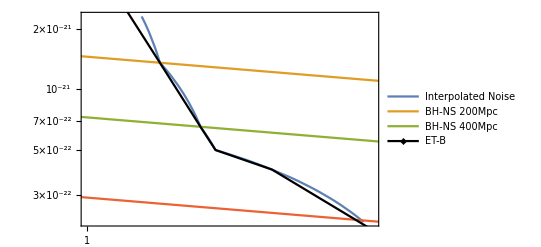

```mathematica
Show[LogLogPlot[{Snoise[[3]][f],2 √f hFD[mBH,f,200Mpc],2 √f hFD[mBH,f,400Mpc],2 √f hFD[mBH,f,1000Mpc]},{f,0.5,200},PlotStyle->{Automatic},PlotRange->{{1.,1.5},{ 2.2 10^-22,0.23 10^-20}},PlotLegends->{"Interpolated Noise","BH-NS 200Mpc","BH-NS 400Mpc"}],ListLogLogPlot[{ASDvFreqData[[3]]},Joined->True,PlotStyle->{{Thick,Black}},AxesLabel->{"GW freq.",None},PlotLegends->PointLegend[{"ET-B"},LegendMarkers->"◆",LegendMarkerSize->{{5,25}}]],ImageSize->400,Frame->True]
```

### Threshold SNR frequencies for M_BH=3.81 at ET-B 2030

```mathematica
fi={1.1,1.175,1.48}; (*Entry frequencies *)
dL={200Mpc, 400Mpc,1000Mpc};
Block[{i=1},{SNR[3,fi[[i]],3.994,dL[[i]],mBH],SNR[3,fi[[i]],5.172,dL[[i]],mBH],SNR[3,fi[[i]],6.43,dL[[i]],mBH]}];
Freqs3p8BHNS200MpcET={3.994,5.172,6.43}
```

{3.994,5.172,6.43}

```mathematica
Block[{i=2},{SNR[3,fi[[i]],6.43,dL[[i]],mBH],SNR[3,fi[[i]],8.65,dL[[i]],mBH],SNR[3,fi[[i]],10.73,dL[[i]],mBH]}];
Freqs3p8BHNS400MpcET={6.43,8.65,10.73}
```

{6.43,8.65,10.73}

```mathematica
Block[{i=3},{SNR[3,fi[[i]],13.32,dL[[i]],mBH],SNR[3,fi[[i]],19.97,dL[[i]],mBH],SNR[3,fi[[i]],24.75,dL[[i]],mBH]}];
Freqs3p8BHNS1GpcET={13.32,19.97,24.75}
```

{13.32,19.97,24.75}

### Advance Warning Times, SNR etc.

```mathematica
SNR3p8BHNS200MpcET=Block[{i=1},SNR[3,fi[[i]],GWfreqIsco[mBH],dL[[i]],mBH]];
SNR3p8BHNS400MpcET=Block[{i=2},SNR[3,fi[[i]],GWfreqIsco[mBH],dL[[i]],mBH]];
SNR3p8BHNS1GpcET=Block[{i=3},SNR[3,fi[[i]],GWfreqIsco[mBH],dL[[i]],mBH]];
Print["Accumulated SNR for 3.8BH-NS(200Mpc) = ",SNR3p8BHNS200MpcET]
Print["Accumulated SNR for 3.8BH-NS(400Mpc) = ",SNR3p8BHNS400MpcET]
Print["Accumulated SNR for 3.8BH-NS(1GMpc) = ",SNR3p8BHNS1GpcET]
Twarn3p8BHNS200MpcET=Tinsp2PN[GWfreqIsco[mBH],Freqs3p8BHNS200MpcET,mBH];
Print["T_warn(200Mpc) = ",Twarn3p8BHNS200MpcET," = ",Twarn3p8BHNS200MpcET/60," minutes"]
Twarn3p8BHNS400MpcET=Tinsp2PN[GWfreqIsco[mBH],Freqs3p8BHNS400MpcET,mBH];
Print["T_warn(400Mpc) = ",Twarn3p8BHNS400MpcET," = ",Twarn3p8BHNS400MpcET/60,"minutes"]
Twarn3p8BHNS1GpcET=Tinsp2PN[GWfreqIsco[mBH],Freqs3p8BHNS1GpcET,mBH];
Print["T_warn(1Gpc) = ",Twarn3p8BHNS1GpcET,"seconds"]
Print["τ_insp(",fi[[1]],"Hz->f_isco) = ",Tinsp2PN[GWfreqIsco[mBH],fi[[1]],mBH]/3600," hours"]
Print["τ_insp(",fi[[2]],"Hz->f_isco) = ",Tinsp2PN[GWfreqIsco[mBH],fi[[2]],mBH]/3600," hours"]
Print["τ_insp(",fi[[3]],"Hz->f_isco) = ",Tinsp2PN[GWfreqIsco[mBH],fi[[3]],mBH]/3600," hours"]
```

Accumulated SNR for 3.8BH-NS(200Mpc) = 381.032

Accumulated SNR for 3.8BH-NS(400Mpc) = 190.516

Accumulated SNR for 3.8BH-NS(1GMpc) = 76.2057

T_warn(200Mpc) = {4164.94,2093.9,1173.35} = {69.4157,34.8983,19.5558} minutes

T_warn(400Mpc) = {1173.35,533.112,300.544} = {19.5558,8.8852,5.00906}minutes

T_warn(1Gpc) = {169.095,57.57,32.5151}seconds

τ_insp(1.1Hz->f_isco) = 35.8196 hours

τ_insp(1.175Hz->f_isco) = 30.0491 hours

τ_insp(1.48Hz->f_isco) = 16.2531 hours

```mathematica
Tinsp2PN[GWfreqIsco[1.4],fi,1.4]/3600
```

{100.71,84.4806,45.6839}

## (27.4 M_sun, a≳0.9) BH - NS

```mathematica
mBH=NSolve[Mc56[m/1.4]/Mc56[1]==3,m][[1,1,2]]
```

27.4029

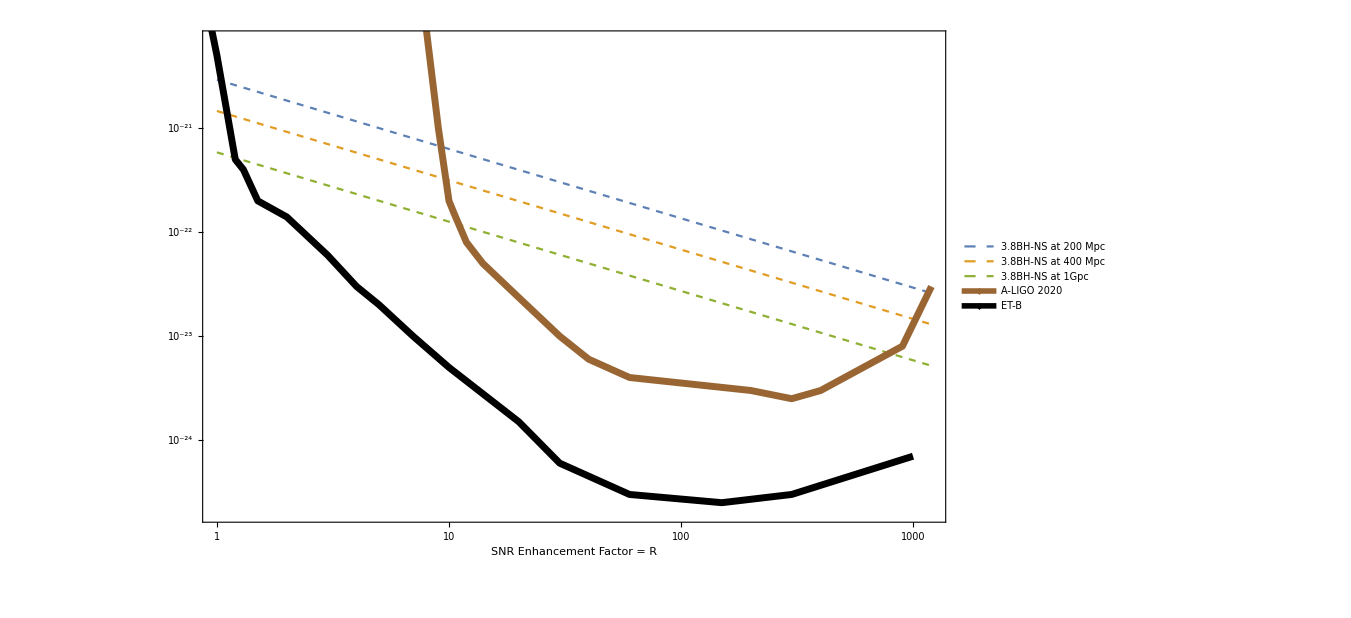

```mathematica
ASDPlotsBHNS=Show[LogLogPlot[{2 √f hFD[mBH,f,200Mpc],2 √f hFD[mBH,f,400Mpc],2 √f hFD[mBH,f,1000Mpc]},{f,1,1200},PlotStyle->{Dashed,Dashed,Dashed},PlotRange->{{1,1200},{2 10^-25,7 10^-21}},PlotLegends->{"3.8BH-NS at 200 Mpc","3.8BH-NS at 400 Mpc","3.8BH-NS at 1Gpc"}],ListLogLogPlot[{ASDvFreqData[[2]],ASDvFreqData[[3]]},Joined->True,PlotStyle->{{Thickness[0.005],Brown},{Thickness[0.005],Black}},AxesLabel->{"GW freq.",None},PlotLegends->PointLegend[{"A-LIGO 2020","ET-B"},LegendMarkers->"◆",LegendMarkerSize->{{5,25}}]],ImageSize->1000,Frame->True,FrameLabel->"SNR Enhancement Factor = "<>ToString[R]]
```

## (27.4 M_sun) BH - NS(200, 400,1000 Mpc) at ET-B 2030

### Picking out the ET-band entrance frequencies for M_BH=27.4

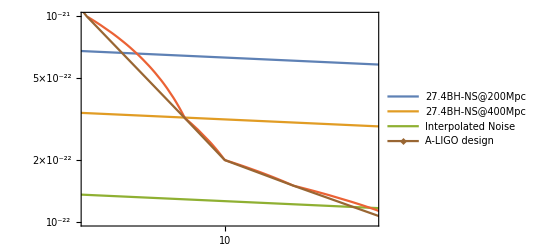

```mathematica
Show[LogLogPlot[{2 √f hFD[mBH,f,200Mpc],2 √f hFD[mBH,f,400Mpc],2 √f hFD[mBH,f,1000Mpc],Snoise[[2]][f]},{f,6,200},PlotStyle->{Automatic},PlotRange->{{9,11.2},{1 10^-22, 10^-21}},PlotLegends->{"27.4BH-NS@200Mpc","27.4BH-NS@400Mpc","Interpolated Noise"}],ListLogLogPlot[{ASDvFreqData[[2]]},Joined->True,PlotStyle->{{Thick,Brown},Black},AxesLabel->{"GW freq.",None},PlotLegends->PointLegend[{"A-LIGO design"},LegendMarkers->"◆",LegendMarkerSize->{{5,25}}]],ImageSize->400,Frame->True]
```

### Threshold SNR frequencies for M_BH=27.4 at A-LIGO2020

```mathematica
fi={9.4,9.7,11.1}; (*Entry frequencies *)
dL={200Mpc, 400Mpc,1000Mpc};
{SNR[2,fi[[1]],22.02,dL[[1]],mBH],SNR[2,fi[[1]],28.91,dL[[1]],mBH],SNR[2,fi[[1]],34.6,dL[[1]],mBH]}
Freqs27p4BHNS200Mpc2020={22.02,28.91,34.6}
```

{10.0004,15.0032,20.007}

{22.02,28.91,34.6}

```mathematica
Block[{i=2},{SNR[2,fi[[i]],34.6,dL[[i]],mBH],SNR[2,fi[[i]],47.38,dL[[i]],mBH],SNR[2,fi[[i]],66.79,dL[[i]],mBH]}]
Freqs27p4BHNS400Mpc2020={34.6,47.38,66.79}
```

{10.0027,14.9993,20.0002}

{34.6,47.38,66.79}

### ADVANCE WARNING TIMES, SNR etc.

```mathematica
SNR27p4BHNS200Mpc2020=SNR[2,fi[[1]],GWfreqIsco[mBH],dL[[1]],mBH];
SNR27p4BHNS400Mpc2020=SNR[2,fi[[1]],GWfreqIsco[mBH],dL[[2]],mBH];
SNR27p4BHNS1Gpc2020=SNR[2,fi[[1]],GWfreqIsco[mBH],dL[[3]],mBH];
Print["Accumulated SNR for 27.4BH-NS(200Mpc) = ",SNR27p4BHNS200Mpc2020]
Print["Accumulated SNR for 27.4BH-NS(400Mpc) = ",SNR27p4BHNS400Mpc2020]
Print["Accumulated SNR for 27.4BH-NS(1Gpc) = ",SNR27p4BHNS1Gpc2020]
Twarn27p4BHNS200Mpc2020=Tinsp2PN[GWfreqIsco[mBH],Freqs27p4BHNS200Mpc2020,mBH];
Twarn27p4BHNS400Mpc2020=Tinsp2PN[GWfreqIsco[mBH],Freqs27p4BHNS400Mpc2020,mBH];
Print["Warning times with SNR thresholds of {10,15,20} = ",Twarn27p4BHNS200Mpc2020," seconds"]
Print["Warning times with SNR thresholds of {10,15,20} = ",Twarn27p4BHNS400Mpc2020," seconds"]
Print["τ_insp(",fi[[1]],"Hz->f_isco) = ",Tinsp2PN[GWfreqIsco[mBH],fi[[1]],mBH]," seconds"]
Print["τ_insp(",fi[[2]],"Hz->f_isco) = ",Tinsp2PN[GWfreqIsco[mBH],fi[[2]],mBH]," seconds"]
Print["τ_insp(",fi[[3]],"Hz->f_isco) = ",Tinsp2PN[GWfreqIsco[mBH],fi[[3]],mBH]," seconds"]
```

Accumulated SNR for 27.4BH-NS(200Mpc) = 52.3493

Accumulated SNR for 27.4BH-NS(400Mpc) = 26.1747

Accumulated SNR for 27.4BH-NS(1Gpc) = 10.4699

Warning times with SNR thresholds of {10,15,20} = {2.50239,1.18501,0.718669} seconds

Warning times with SNR thresholds of {10,15,20} = {0.718669,0.29337,0.104159} seconds

τ_insp(9.4Hz->f_isco) = 24.8506 seconds

τ_insp(9.7Hz->f_isco) = 22.8464 seconds

τ_insp(11.1Hz->f_isco) = 15.9195 seconds

## (27.4 M_sun) BH - NS(200, 400 Mpc) at A-LIGO2020

### Picking out the LIGO-band entrance frequencies for M_BH=27.4

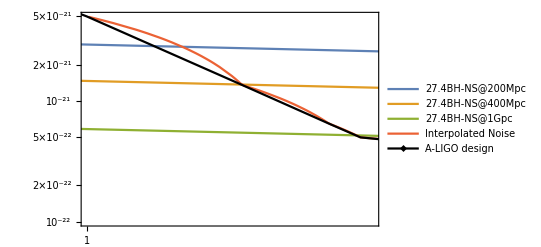

```mathematica
Show[LogLogPlot[{2 √f hFD[mBH,f,200Mpc],2 √f hFD[mBH,f,400Mpc],2 √f hFD[mBH,f,1000Mpc],Snoise[[3]][f]},{f,0.5,200},PlotStyle->{Automatic},PlotRange->{{1,1.21},{1 10^-22,5 10^-21}},PlotLegends->{"27.4BH-NS@200Mpc","27.4BH-NS@400Mpc","27.4BH-NS@1Gpc","Interpolated Noise"}],ListLogLogPlot[{ASDvFreqData[[3]]},Joined->True,PlotStyle->{{Thick,Black}},AxesLabel->{"GW freq.",None},PlotLegends->PointLegend[{"A-LIGO design"},LegendMarkers->"◆",LegendMarkerSize->{{5,25}}]],ImageSize->400,Frame->True]
```

### Threshold SNR frequencies for M_BH=27.4 at A-LIGO2020

```mathematica
fi={1.07,1.11,1.2}; (*Entry frequencies *)
dL={200Mpc, 400Mpc,1000Mpc};
{SNR[3,fi[[1]],2.505,dL[[1]],mBH],SNR[3,fi[[1]],3.32,dL[[1]],mBH],SNR[3,fi[[1]],3.98,dL[[1]],mBH]}
Freqs27p4BHNS200MpcET={2.505,3.32,3.98}
```

{10.0015,15.0667,20.0405}

{2.505,3.32,3.98}

```mathematica
Block[{i=2},{SNR[3,fi[[i]],3.98,dL[[i]],mBH],SNR[3,fi[[i]],5.15,dL[[i]],mBH],SNR[3,fi[[i]],6.4,dL[[i]],mBH]}]
Freqs27p4BHNS400MpcET={3.98,5.15,6.4}
```

{10.0193,15.0327,20.0451}

{3.98,5.15,6.4}

```mathematica
Block[{i=3},{SNR[3,fi[[i]],7.5,dL[[i]],mBH],SNR[3,fi[[i]],10.2,dL[[i]],mBH],SNR[3,fi[[i]],13.2,dL[[i]],mBH]}];
Freqs27p4BHNS1GpcET={7.5,10.2,13.2}
```

{7.5,10.2,13.2}

### ADVANCE WARNING TIMES, SNR etc.

```mathematica
SNR27p4BHNS200MpcET=SNR[3,fi[[1]],GWfreqIsco[mBH],dL[[1]],mBH];
SNR27p4BHNS400MpcET=SNR[3,fi[[1]],GWfreqIsco[mBH],dL[[2]],mBH];
SNR27p4BHNS1GpcET=SNR[3,fi[[1]],GWfreqIsco[mBH],dL[[3]],mBH];
Print["Accumulated SNR for 27.4BH-NS(200Mpc) = ",SNR27p4BHNS200MpcET]
Print["Accumulated SNR for 27.4BH-NS(400Mpc) = ",SNR27p4BHNS400MpcET]
Print["Accumulated SNR for 27.4BH-NS(1Gpc) = ",SNR27p4BHNS1GpcET]
Twarn27p4BHNS200MpcET=Tinsp2PN[GWfreqIsco[mBH],Freqs27p4BHNS200MpcET,mBH];
Twarn27p4BHNS400MpcET=Tinsp2PN[GWfreqIsco[mBH],Freqs27p4BHNS400MpcET,mBH];
Twarn27p4BHNS1GpcET=Tinsp2PN[GWfreqIsco[mBH],Freqs27p4BHNS1GpcET,mBH];
Print["Warning times with SNR thresholds of {10,15,20} = ",Twarn27p4BHNS200MpcET/60," minutes"]
Print["Warning times with SNR thresholds of {10,15,20} = ",Twarn27p4BHNS400MpcET/60," minutes"]
Print["Warning times with SNR thresholds of {10,15,20} = ",Twarn27p4BHNS1GpcET," seconds"]
Print["τ_insp(",fi[[1]],"Hz->f_isco) = ",Tinsp2PN[GWfreqIsco[mBH],fi[[1]],mBH]/60," minutes"]
Print["τ_insp(",fi[[2]],"Hz->f_isco) = ",Tinsp2PN[GWfreqIsco[mBH],fi[[2]],mBH]/60," minutes"]
Print["τ_insp(",fi[[3]],"Hz->f_isco) = ",Tinsp2PN[GWfreqIsco[mBH],fi[[3]],mBH]/60," minutes"]
```

Accumulated SNR for 27.4BH-NS(200Mpc) = 712.928

Accumulated SNR for 27.4BH-NS(400Mpc) = 356.464

Accumulated SNR for 27.4BH-NS(1Gpc) = 142.586

Warning times with SNR thresholds of {10,15,20} = {14.0567,6.64385,4.1005} minutes

Warning times with SNR thresholds of {10,15,20} = {4.1005,2.06424,1.15658} minutes

Warning times with SNR thresholds of {10,15,20} = {45.4452,19.9692,9.99628} seconds

τ_insp(1.07Hz->f_isco) = 135.055 minutes

τ_insp(1.11Hz->f_isco) = 122.493 minutes

τ_insp(1.2Hz->f_isco) = 99.5508 minutes